```mathematica
(*Data[i_]:=Import[FileNameJoin[{NotebookDirectory[],"L="<>ToString@i<>",P=(08,12),n=10000PLANE,EM2.out"}]]
Data2[i_]:=Import[FileNameJoin[{NotebookDirectory[],"L="<>ToString@i<>",P=(08,12),n=100PLANE,EM2(test).out"}]]
EM2Data[i_]:=Import[FileNameJoin[{NotebookDirectory[],"L="<>ToString@i<>",P=(04,08),n=10000PLANE,EM2.out"}]]
testData:=Import[FileNameJoin[{NotebookDirectory[],"test1.out"}]]*)
testData:=Import[FileNameJoin[{NotebookDirectory[],"test.out"}]]
```

```mathematica
normalizeData[data_,n_]:=DeleteCases[data,Except[{_,_,_,_Integer}]]/.{{a_,b_,c_,d_}:>{a,b,c,(1-d/n)//N},{}->Nothing};
```

```mathematica
filterData[nn_,data_,n_]:=Drop[data,1]/.{{a_,b_,c_,d_}:>{a,b,c,p[nn,d/n]//N},{}->Nothing};
```

```mathematica
(*Gate noise*)
```

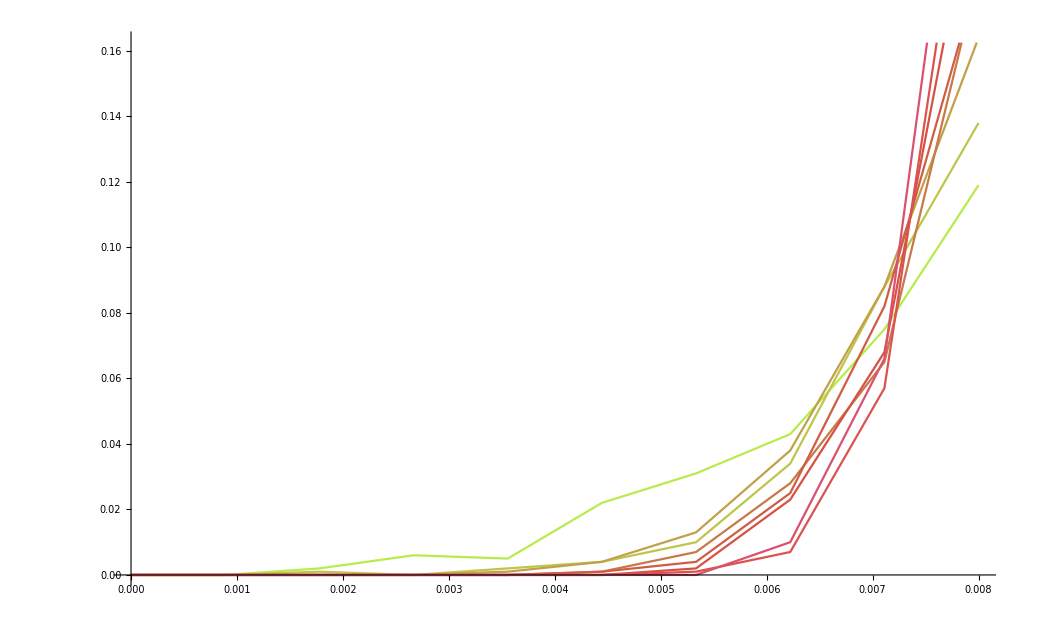

```mathematica
ListLinePlot[Map[#[[{2,4}]]&,Values@GroupBy[normalizeData[testData,1000],First],{2}],PlotStyle->Table[ColorData["NeonColors"][i],{i,0,1,0.1}]]
```

```mathematica
Remove[n]
```

```mathematica
nn[n_]:=Sum[(n!)/((n-k)!k!)p^k(1-p)^(n-k),{k,1,n,2}]
```

```mathematica
nn[5]
```

{5 (1-p)^4 p+10 (1-p)^2 p^3+p^5}

```mathematica
nnn[n_]:=Sum[(n!)/((n-k)!k!)nn[n]^k(1-nn[n])^(n-k),{k,0,Floor[(n-1)/2]}]
```

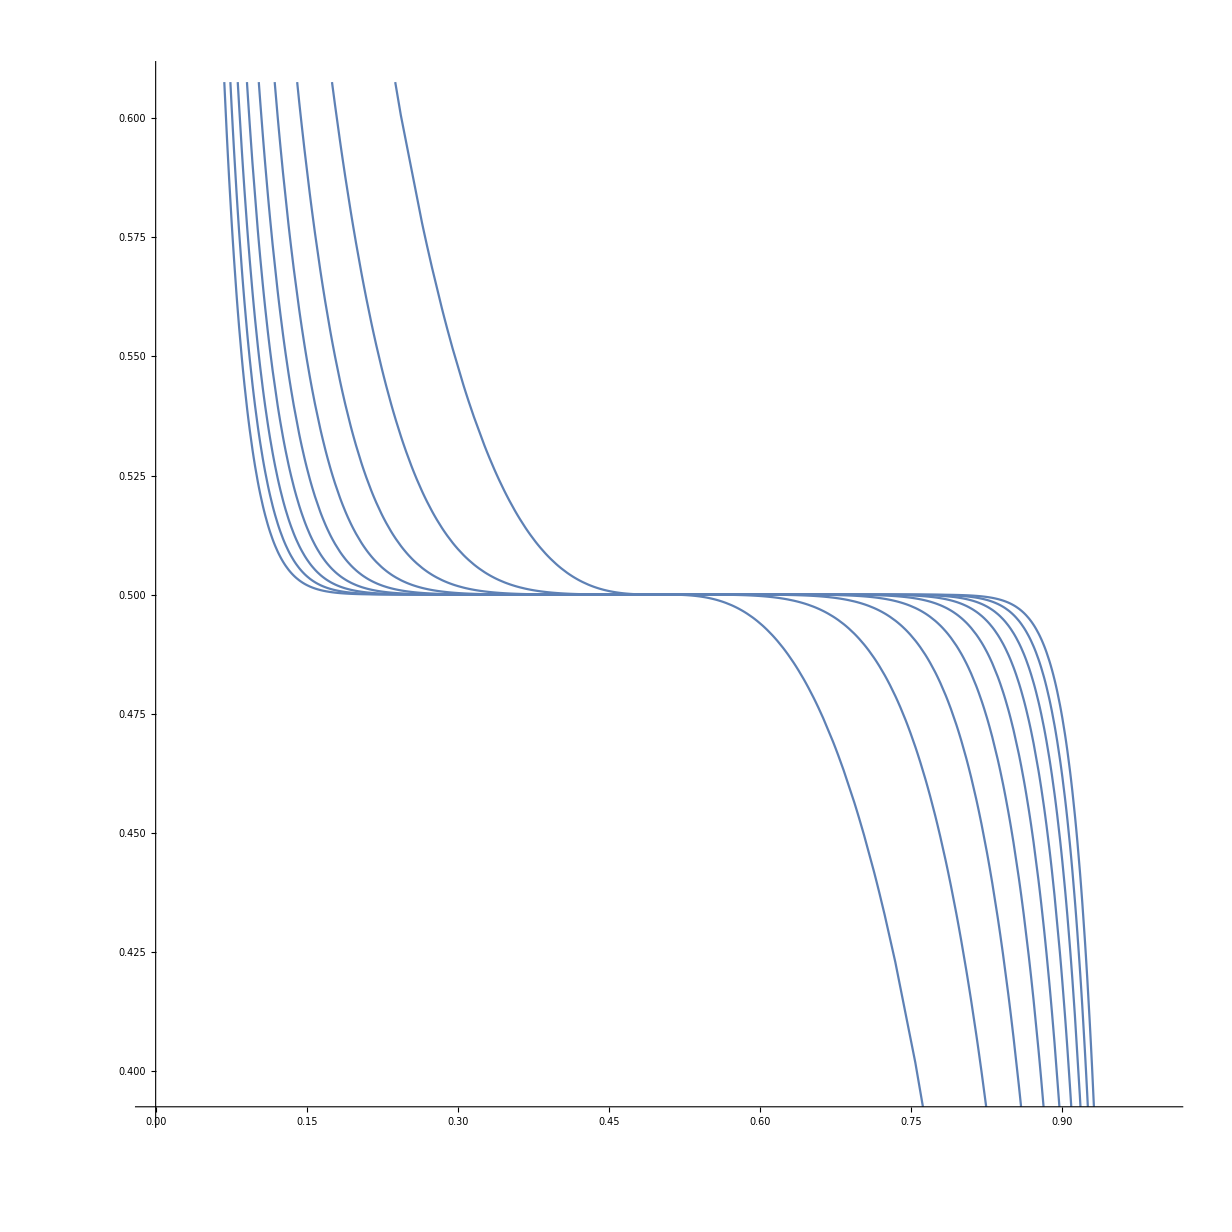

```mathematica
Plot[Table[nnn[i],{i,3,19,2}],{p,0,1},AspectRatio->1]
```

```mathematica
np[3]
```

(1-p)^3+3 (1-p)^2 p

```mathematica
(*Majority Vote*)nm[n_,p_]:=Sum[(n!)/((n-k)!k!)p^(n-k)(1-p)^k,{k,0,Floor[(n-1)/2]}]
```

```mathematica
(*Parity*)np[n_,p_]:=Sum[(n!)/((n-k)!k!)p^k(1-p)^(n-k),{k,1,n,2}]
```

```mathematica
1-np[5]
```

1-(1-p)^5-5 (1-p)^4 p-10 (1-p)^3 p^2

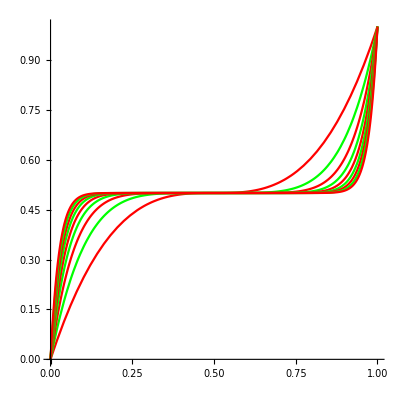

```mathematica
Plot[Evaluate@Table[{np[i,p]},{i,3,19,2}],{p,0,1},PlotRange->{0,1},AspectRatio->1,PlotStyle->{Red,Green}]
```

General::munfl: (1.95163×10^-34)^11 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.95163×10^-34)^13 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.95163×10^-34)^15 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.16917×10^-42)^9 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

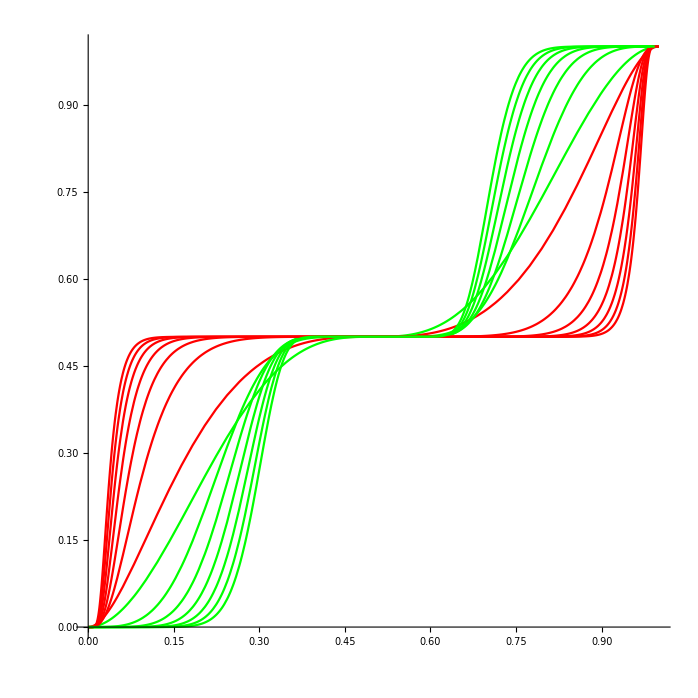

```mathematica
Plot[Evaluate@Table[{nm[i,np[i,p]],np[i,nm[i,p]]},{i,3,30,4}],{p,0,1},PlotRange->{0,1},AspectRatio->1,PlotStyle->{Red,Green}]
```

```mathematica
nbig[n_,p_]:=Sum[(n!)/((n-k)!k!)np[n]^k(1-np[n])^(n-k),{k,0,Floor[(n-1)/2]}]
```

```mathematica
nsmall[n_]:=Sum[(n!)/((n-k)!k!)np[n]^k(1-np[n])^(n-k),{k,0,Floor[(n-1)/2]}]
```

```mathematica
(69+74.5+72+74+73+70)/(6*75)*55/100+45.5/50*15/100+48/50*15/100+85/100*15/100
```

0.936611

```mathematica
(69+74.5+72+74+73+70)/(6*75)*55/70+85/100*15/70
```

0.937302